```mathematica
totdrifts = {};
drifts={0,0};
imstack = Table[Print[count];
positions = Flatten[Table[{x,y},{y,( Ceiling[count/4]-1)20+17,250,20},{x,17,250,20}],1];
Do[AppendTo[positions,{128+i,128}];AppendTo[positions,{128,128+i}];,{i,-10,10,4}];
imout=RandomVariate[NormalDistribution[500,100],{256,256}];
AppendTo[totdrifts,-Reverse[drifts]];
Do[imout[[x,y]] += N[ (positions[[i,1]])E^(-(x-x0)^2/(2 σ^2))E^(-(y-y0)^2/(2 σ^2))/.x0->(positions[[i,1]]+drifts[[1]])/.y0->(positions[[i,2]]+drifts[[2]])/.σ->N[Sqrt[10/π]]],{i,1,Length[positions]},{x,Max[Round[(positions[[i,1]]+drifts[[1]])-6],1],Min[Round[(positions[[i,1]]+drifts[[1]])+6],256]},{y,Max[Round[(positions[[i,2]]+drifts[[2]])-6],1],Min[Round[(positions[[i,2]]+drifts[[2]])+6],256]}];
drifts += RandomVariate[NormalDistribution[0,1],2];
Image[imout/2^16],{count,1,50}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

```mathematica
Export["Y:\\Boecking\\James_Walsh\\Jim_v5_3\\Example_Data\\Jim_Test_Array_Example.tif",imstack];
```

```mathematica
Export["Y:\\Boecking\\James_Walsh\\Jim_v5_3\\Example_Data\\Jim_Test_Array_Example_drifts.csv",Prepend[totdrifts,{"X Drifts","Y Drifts"}]];
```

```mathematica
totdrifts
```

{{0,0},{0.305893,-0.687214},{1.03927,-0.975786},{1.65108,-1.77439},{1.4994,-2.6527},{2.24535,-2.61449},{2.3702,-2.95349},{1.83322,-3.98857},{2.47974,-2.88872},{4.25484,-4.35634},{3.42838,-4.43226},{3.14756,-3.63446},{3.29792,-5.04408},{4.20443,-3.40973},{5.17337,-3.56719},{5.82844,-1.31042},{4.853,0.250905},{5.30696,1.19783},{3.68954,0.763763},{2.99663,0.244963},{4.00844,0.809734},{4.44128,1.54356},{3.95844,3.04083},{4.70525,2.89035},{4.38038,2.80498},{4.36269,1.81547},{5.60864,1.27178},{7.81418,4.32306},{10.4053,4.78525},{9.97316,4.67774},{10.9623,4.35808},{11.442,4.00665},{8.91176,2.93098},{8.07759,3.74956},{8.40813,4.31797},{7.7018,3.68913},{7.3041,1.74958},{7.75389,3.52977},{6.22206,2.56492},{7.79735,1.72079},{7.73486,0.812647},{9.13166,-2.06591},{8.85053,-2.53959},{8.10837,-2.7919},{7.97431,-2.19723},{8.73341,-2.85805},{10.8548,-0.949355},{11.7036,-1.83278},{11.4693,-4.02132},{11.7874,-4.92288}}

```mathematica
Max[totdrifts]
```

11.7874

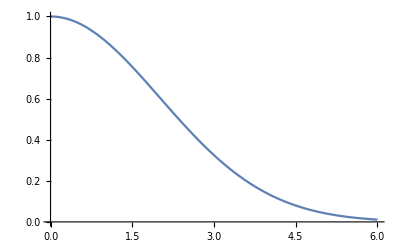

```mathematica
Plot[E^(-(x)^2/(2 σ^2))/.σ->2,{x,0,6}]
```